```mathematica
Lx=60;
Ly=60;
A=Lx*Ly;
```

```mathematica
m0 = 1;
```

```mathematica
LineChernListP1 = Import["/media/archisman/Home Partition/archisman/Documents/GitHub/quasicrystals/local_chern_number_data/dataPTB/dataPTBlocalChernSitesOnLineLx=60Ly=60m0=1Xup=8Xdn=4PartsPerThousand=77Irrational.dat"];
```

```mathematica
LineChernListP2 = Import["/media/archisman/Home Partition/archisman/Documents/GitHub/quasicrystals/local_chern_number_data/dataPTB/dataPTBlocalChernSitesOnLineLx=60Ly=60m0=-1Xup=8Xdn=4PartsPerThousand=77Irrational.dat"];
```

```mathematica
list1 = Table[LineChernListP1[[ii]][[3]],{ii,1,Lx}]
```

{-20.0167,1.01254,0.98146,0.979377,0.982853,0.983278,0.981697,0.983709,0.981691,0.983171,0.982982,0.98036,0.982976,0.983169,0.981698,0.9837,0.981702,0.983209,0.98321,0.981703,0.9837,0.981696,0.983167,0.982975,0.980358,0.982975,0.983167,0.981697,0.9837,0.981697,0.983167,0.982975,0.980358,0.982975,0.983167,0.981697,0.9837,0.981703,0.98321,0.983209,0.981703,0.9837,0.981697,0.983168,0.982975,0.980359,0.982978,0.983168,0.981694,0.983703,0.981705,0.98323,0.983224,0.981682,0.983664,0.981639,0.985121,0.98931,0.980286,-15.4106}

```mathematica
list2 = Table[LineChernListP2[[ii]][[3]],{ii,1,Lx}]
```

{20.0167,-1.01254,-0.98146,-0.979377,-0.982853,-0.983278,-0.981697,-0.983709,-0.981691,-0.983171,-0.982982,-0.98036,-0.982976,-0.983169,-0.981698,-0.9837,-0.981702,-0.983209,-0.98321,-0.981703,-0.9837,-0.981696,-0.983167,-0.982975,-0.980358,-0.982975,-0.983167,-0.981697,-0.9837,-0.981697,-0.983167,-0.982975,-0.980358,-0.982975,-0.983167,-0.981697,-0.9837,-0.981703,-0.98321,-0.983209,-0.981703,-0.9837,-0.981697,-0.983168,-0.982975,-0.980359,-0.982978,-0.983168,-0.981694,-0.983703,-0.981705,-0.98323,-0.983224,-0.981682,-0.983664,-0.981639,-0.985121,-0.98931,-0.980286,15.4106}

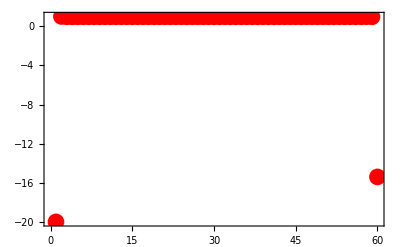

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

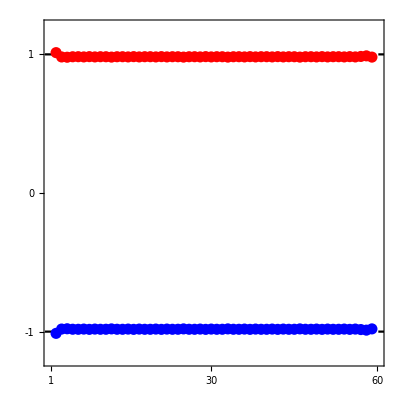

```mathematica
Show[Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.2,1.2}},Frame->True,Axes->False],
ListPlot[list1,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{0,"0"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1]
```